```mathematica
a=0.0001;
d=0.000356;
D1=0.5;
D2=0.5;
λ=630*10^-9;
x=0;

f[z_]:=Abs[NIntegrate[ⅇ^(ⅈ π (x-y)^2/(D1 λ))ⅇ^(ⅈ π (z-y)^2/(D2 λ)),{y,-d/2-a/2,-d/2+a/2}]+NIntegrate[ⅇ^(ⅈ π (x-y)^2/(D1 λ))ⅇ^(ⅈ π (z-y)^2/(D2 λ)),{y,d/2-a/2,d/2+a/2}]]^2
```

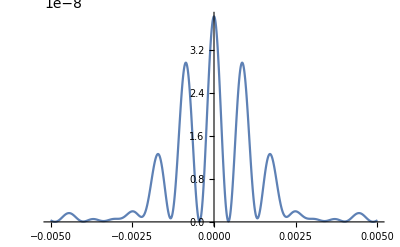

```mathematica
Plot[f[z],{z,-0.005,0.005}]
```